# Sign method

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedInitialSign";
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30-4}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-4,30-4}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

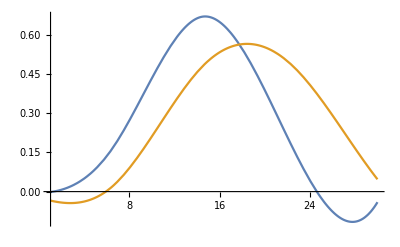

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,3];
pyrf2=pyrFuncGen[line2,3];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}]
```

## Pyramidal Flow 1D

### PyrUpgrade1D

```mathematica
pyrf1=pyrFuncGen[line1,5];
pyrf2=pyrFuncGen[line2,5];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];
Plot[{pyrf12[[5,1,1]][x],pyrf12[[5,2,1]][x]},{x,1,30}];
```

```mathematica
findPrevNext[p0_,csign_,{dfline1_,dfline2_}]:=Block[{continue,notcontinue, resFunc, sumFunc,r1left,rleft,r2left,r1right,r2right,rright},(

continue1[p_]:=Sign[dfline1[p]*dfline2[p0]]==-1;

continue2[p_]:=Sign[dfline1[p0]*dfline2[p]]==-1;

upFunc1[p_]:=p-Sign[dfline1[p0]]*csign[[1]]*0.1;

upFunc2[p_]:=p-Sign[dfline2[p0]]*csign[[2]]*0.1;


If[dfline1[p0]>dfline2[p0],

r2=NestWhile[upFunc2,p0,continue2,1,50];
Return[{0.,-Sign[dfline2[p0]]*(Sqrt[(p0-r2)^2])}]
,
r1=NestWhile[upFunc1,p0,continue1,1,50];
Return[{-Sign[dfline1[p0]]*(Sqrt[(p0-r1)^2]),0.}]
];


)];
```

```mathematica
findPrevNext[16,{-1,-1}, pyrf12[[5,All,2]]]
```

{3.9,0.}

```mathematica
16-1.6
```

14.4

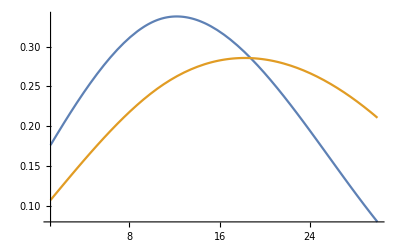

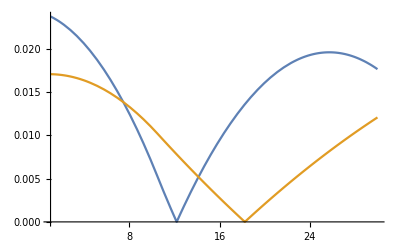

```mathematica
Plot[{pyrf12[[5,1,1]][x],pyrf12[[5,2,1]][x]},{x,1,30}]
Plot[{Abs[pyrf12[[5,1,2]][x]],Abs[pyrf12[[5,2,2]][x]]},{x,1,30}]
```

```mathematica
(* Input-> {{initial values for v1, v2 and status}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status} *)
PyrUpgrade1D[{v1_,v2_,status_,e_,dv1sign_,dv2sign_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedInitialSign"]:=Block[{fric1,fric2,p1, p2, c,d1,d2,dv1,dv2,newdv1sign, newdv2sign},(

p1=(p0-dv1sign)-v1;
p2=(p0+dv2sign)+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=0.5*dfline1'[p1]; 
fric2=0.5*dfline2'[p2];

(* magnitude error *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),
If[e<2,Return[{v1,v2,"mag",e+1,dv1sign,dv2sign}],Return[{0.,0.,"mag",e,0.,0.}]]];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, 
If[e<2,

(* if p at initial position and failed... *)
If[((p0-dv1sign)==p1 &&(p0+dv2sign)==p2 ),


(* we feed new dv1sign... *)
csign={Sign[(fline1[p0]-c)],Sign[(c-fline2[p0])]};
{newdv1sign,newdv2sign}=findPrevNext[p0, csign,{dfline1,dfline2}];

Return[PyrUpgrade1D[{v1,v2,"oksign",e,newdv1sign, newdv2sign},p0, {{fline1,dfline1} ,{fline2,dfline2}}, threshold,"ConstrainedInitialSign"]],

Return[PyrUpgrade1D[{v1,v2,"oksign",e,dv1sign,dv2sign},p0, {{fline1,dfline1} ,{fline2,dfline2}}, threshold,"ConstrainedInitialSign"]]
]
,
Return[{0.,0.,"sign",e,0.,0.}]
]
];

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.001,"converged","ok"],e,dv1sign,dv2sign}
)];

(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
PyrUpgrade1D[{v1_,v2_,"oksign",e_,dv1sign_,dv2sign_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedInitialSign"]:=Block[{fric1,fric2,p1,p2,c,d1,d2,dv1,dv2,r0},(

p1=(p0-dv1sign)-v1;
p2=(p0+dv2sign)+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=0.5*dfline1'[p1];
fric2=0.5*dfline2'[p2];

(*{Null,Null}*)
(* magnitude *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<2,Return[{v1,v2,"mag",e+1,dv1sign,dv2sign}],Return[{0.,0.,"mag",e,0.,0.}]]];

(*{Null,Null}*)
(* d1 and d2 have to be the same sign *)
 If[d1*d2 <0, If[e<2,Return[{v1,v2,"sign",e+1,dv1sign,dv2sign}],Return[{0.,0.,"sign",e,0.,0.}]]]; 

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.001,"converged","oksign"],e,dv1sign,dv2sign}
)];


PyrUpgrade1D[{v1_,v2_,status_,2,dv1sign_,dv2sign_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedInitialSign"]:=Return[{0.,0.,status,2,0.,0.}];

PyrUpgrade1D[{v1_,v2_,"sign",e_,dv1sign_,dv2sign_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedInitialSign"]:=Return[{v1,v2,"sign",e,dv1sign,dv2sign}];

PyrUpgrade1D[{v1_,v2_,"mag",e_,dv1sign_,dv2sign_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedInitialSign"]:=Return[{v1,v2,"mag",e,dv1sign,dv2sign}];

PyrUpgrade1D[{v1_,v2_,"flip",e_,dv1sign_,dv2sign_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedInitialSign"]:=Return[{v1,v2,"flip",e,dv1sign,dv2sign}];

PyrUpgrade1D::usage="
Function to update values of v1 and v2 with Constrained standards
Input→ [{v1,v2,status,e},p0,{{f1,df1},{f2,df2},threshold}
Output-> {v1,v2,status}
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
e= counts the amount of constraints not met
p0= point of interest
{f1,df1}={function 1, derivative of function 1}
{f2,df2}={function 2, derivative of function 2}
threshold= threshold to respect magnitude constraint
";
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e,dv1sign,dv2sign}={0.,0.,"ok",0.,0.,0.};
i=0;
p=16;
```

```mathematica
n=5;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e,dv1sign,dv2sign}=PyrUpgrade1D[{v1,v2,status,e,dv1sign,dv2sign},p, pyrf12[[n]],0.0001,noteBookMode]
```

{6.76073,5.3262,oksign,0.,5.,0.}

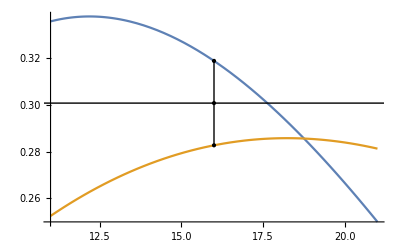

```mathematica
(* see *)
seePlot[p,5,{v1+dv1sign,v2+dv2sign},pyrf12[[n]]]
```

### PyrFlow1D

pyrfunctions : all levels of pyramid. {l1,l2,l3,l4,...} or {l1}

```mathematica
PyrFlow1D[i_, p0_, pyrfunctions_,threshold_,"ConstrainedInitialSign"]:=Block[{v1, v2,c,d,dd,cc,status,e,dv1sign,iterTable,updateValues},(
c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e, dv1sign, dv2sign}*)
updateValues={0.,0.,"ok",0.,0.,0.};

Do[
(* compute at this scale, using current motion estimate *)
If[updateValues[[4]]<2,updateValues[[3]]="ok",updateValues={0.,0.,updateValues[[3]],2.,0.,0.}];

iterTable=Table[
updateValues=PyrUpgrade1D[updateValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedInitialSign"];

,{j,1,i}];

c=c-1;
,{f,1,Length[pyrfunctions]}];

{updateValues[[1]]+updateValues[[-2]], updateValues[[2]]+updateValues[[-1]],updateValues[[3]]}
)];

PyrFlow1D::usage="
Function to update values of v1 and v2 over all levels of a pyramidal function representation
with OverConstrained standards.
Input→ [i, p0, pyrfunctions, threshold]
Output-> {v1, v2, status,e}
i= number of iterations
p0= point of interest
pyrfunctions= list with the dimensions of {pyrlvl, number of image(1 or 2), kind of function(f or df)}
where pyrlvl is the pyramidal level
threshold= threshold to respect magnitude constraint
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
e= Counts the amount of times the constraints were not met
";
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
(* Initializing values *)
{v1, v2}={0.,0.};
i=10;
p=16;

(* m-> max lvl, n-> min lvl *)
m=5;
n=5;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

{11.7607,5.3262,sign}

{17.0869,sign}

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[m]]]
```

-Graphics-

## Graphics for All pixels

### All Pixel Graphics

#### Test

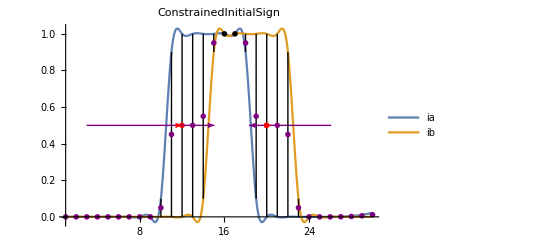

```mathematica
tes1=lineTest[Range[1,Length[line1]],pyrf12[[5;;5]],0.001,noteBookMode];
seeAllLine[Range[1,30],pyrf12[[1;;1]],0.01,noteBookMode]
```

## Graphics for One pixel

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_, p0_,v0_, pyrfunctions_,threshold_,"ConstrainedInitialSign"]:=Block[{v1, v2,c,status,iterTable,updateValues},(

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e, dv1sign, dv2sign}*)
updateValues={v0[[1]],v0[[2]],"ok",0.,0.,0.};

Table[
(* compute at this scale, using current motion estimate *)
If[updateValues[[4]]<2,updateValues[[3]]="ok",updateValues={0.,0.,updateValues[[3]],2.,0.,0.}];

iterTable=Table[
updateValues=PyrUpgrade1D[updateValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedInitialSign"];

{updateValues[[1]]+updateValues[[-2]], updateValues[[2]]+updateValues[[-1]],updateValues[[3]]}
,{j,1,i*2}];

c=c-1;

iterTable
,{f,1,Length[pyrfunctions]}]
)];
```

#### Test

```mathematica
iter=PyrFlow1DIter[10, 11,{0.,0.}, pyrf12[[1 ;;3]],0.001,noteBookMode]
```

{{{1.43452,4.12252,ok},{1.49121,2.56951,ok},{1.49596,2.50918,ok},{1.49636,2.50413,ok},{1.4964,2.5037,converged},{1.4964,2.50367,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged},{1.4964,2.50366,converged}},{{1.0009,2.99911,ok},{0.907023,3.09298,ok},{0.893063,3.10694,ok},{0.891236,3.10876,ok},{0.891002,3.109,converged},{0.890972,3.10903,converged},{0.890969,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged},{0.890968,3.10903,converged}},{{0.670025,3.32998,ok},{0.577329,3.42267,ok},{0.556371,3.44363,ok},{0.554022,3.44598,ok},{0.553826,3.44617,converged},{0.553811,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged},{0.553809,3.44619,converged}}}